# I Bessel function table creator.

1/2 (BesselI[-1+nn,x]+BesselI[1+nn,x])

{1.48552863110618×10^605,1.48499723107978×10^605,1.48340417154813×10^605,1.48075287007392×10^605}

{1.48499723107978×10^605,1.48446640132716×10^605,1.48287505057685×10^605,1.48022659028188×10^605}

{0.0106707593524,0.0106669422319,0.0106554990631,0.0106364543948}

{0.0106669,0.0106631,0.0106517,0.0106327}

{1.48499723107978×10^605,1.48446640132716×10^605,1.48287505057685×10^605,1.48022659028188×10^605}

-Graphics-

-Graphics-

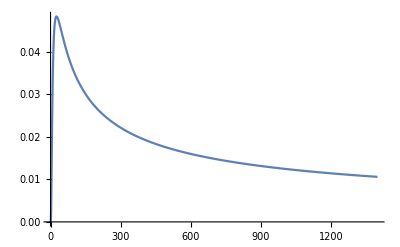

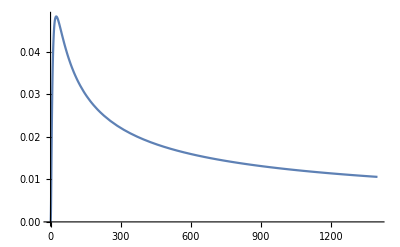

```mathematica
n:=5;range:=1398;
f[n_,arg_]:=BesselI[n,arg];
D[BesselI[nn,x],x]
fP[n_,arg_]:=0.5*(BesselI[-1+n,arg]+BesselI[1+n,arg]);
expf[n_,arg_]:=Exp[-arg]*f[n,arg];
expfP[n_,arg_]:=Exp[-arg]*fP[n,arg];
nRange:=Table[i,{i,0,n-2}]
N[f[nRange,range]]
N[fP[nRange,range]]
N[expf[nRange,range]]
N[expfP[nRange,range]]
Block[{$MaxExtraPrecision=1000},N[fP[nRange,range]-f[nRange,range]]]
Plot[f[n,arg],{arg,0,range}]
Plot[fP[n,arg],{arg,0,range}]
Plot[expf[n,arg],{arg,0,range}]
Plot[expfP[n,arg],{arg,0,range}]
```

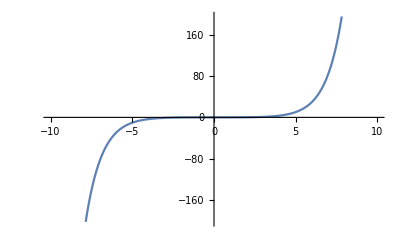

```mathematica
Plot[f[n,arg],{arg,-range,range},PlotPoints->100,MaxRecursion->10]
```

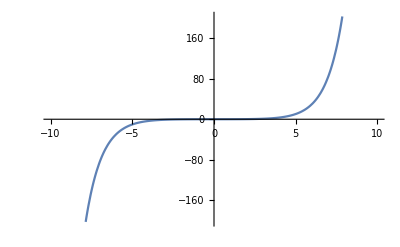

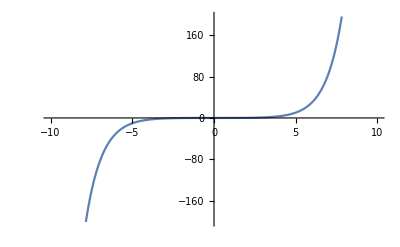

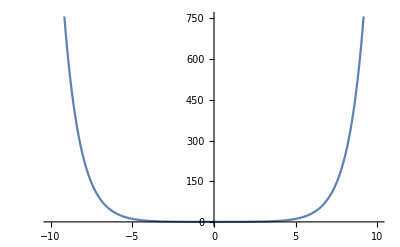

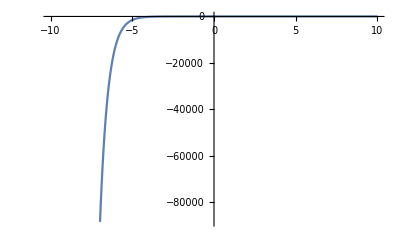

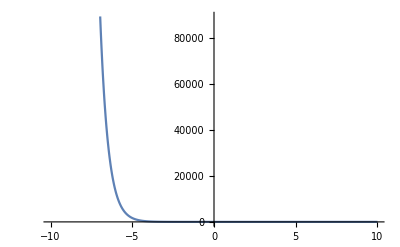

```mathematica
Plot[f[n,arg],{arg,-range,range},PlotPoints->11,MaxRecursion->10]
```

```mathematica
N[BesselI[5,1000]]
```

2.45479311244708×10^432